## Phases and Coefficiets

Prepare

```mathematica
imgsize=700;
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter

```mathematica
ClearAll[n1M,n2M,k1M,k2M,a1M,a2M,phaseList,coeffList,coeffListRe,coeffListIm,coeffListAbs,list0,list1,list2,list3,list4,n2List1,n1List2,n2List3,n1List4,meshStyle,parList,k1A,k2A,a1A,a2A,range,range2];
```

```mathematica
Get["../../neuPackage/neutrino.wl"]
```

Parameters

```mathematica
thetamV=Pi/5;
k1V=0.3;
k2V=0.7;
a1V=0.1(*0.1(k1V)^(-5/3);*);
a2V=0.1(*0.1(k2V)^(-5/3)*);
phi1V=0;
phi2V=0;
```

```mathematica
omegaV=3.75*10^(-17)(*MeV*);(*For MeV neutrinos*)
thetaV=ArcSin[√0.3/2];
```

```mathematica
n2Fun[n1_,k1_,k2_]:=Round[(1-n1*k1)/k2];
```

Width

```mathematica
width2Freq[-1,-1,k1V,k2V,a1V,a2V,thetamV]
```

0.00139729

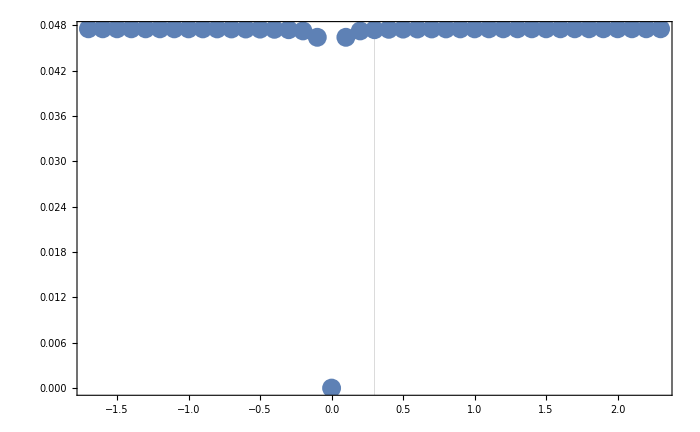

```mathematica
ListPlot[Table[{k1V+x,width2Freq[0,1,k1V+x,k2V,a1V,a2V,thetamV]},{x,-2,2,0.1}],PlotRange->Full,GridLines->{{k1V},None},ImageSize->imgsize,Frame->True]
```

```mathematica
qDis2Width[1,-1,k1V,k2V,a1V,a2V,thetamV]
```

708.477

```mathematica
Module[{n1M,n2M},
n1M=1;
n2M=1;

Grid[{{distanceFun[n1M,n2M,k1V,k2V]},{width2Freq[n1M,n2M,k1V,k2V,a1V,a2V,thetamV]},{qDis2Width[n1M,n2M,k1V,k2V,a1V,a2V,thetamV]}}]
]
```

0.
0.
0

Coefficients

Test result for some example data.

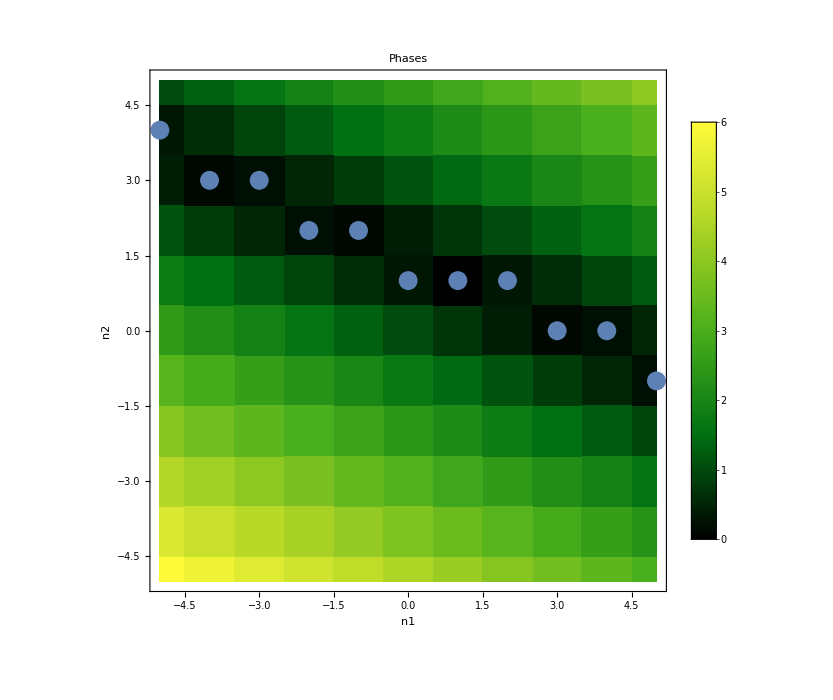
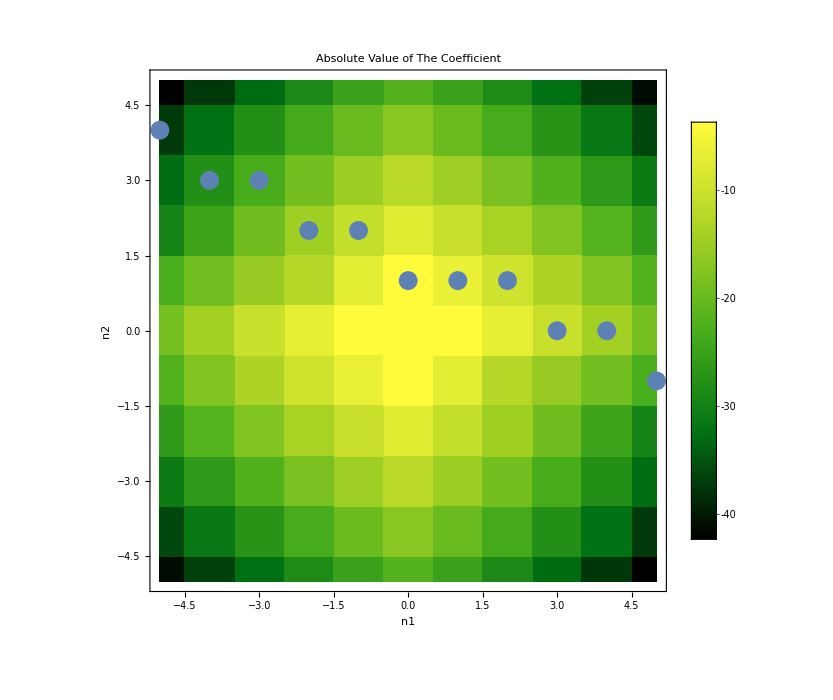
-Graphics- | -Graphics-
-Graphics- | -Graphics-
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{k1A,k2A,a1A,a2A,thetamA,range,range2,order,endpoint},
k1A=k1V;
k2A=k2V;
a1A=a1V;(*0.1(k1A)^(-5/3);*)
a2A=a2V;(*(k2A)^(-5/3);*)
thetamA=thetamV;
range=5;
range2=5;
order=5;
endpoint=800;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,thetamA,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,thetamA,range,range2]
},{
Table[Show[pltN[k1A,k2A,a1A,a2A,thetamA,endpoint,Red],plt0Orders[k1A,k2A,a1A,a2A,thetamA,endpoint,ord,0,ToString[ord]<>",0;",Black](*,pltAll[k1,k2,a1,a2,order,Magenta]*),PlotRange->All],{ord,0,order}]
}
}]
]
(*Export["export/stimulated-2-freq-coef-non-approx-a2-larger-non-mesh.png",%]*)
```

## Compare with Previous calculations

We had a case where adding 1 and 2 will change the result but adding 3 doesn’t. They match the exact data when 4th order is added.

### First Case

k1=0.3;
k2=0.99;
a1=0.2*0.1(k1)^(-5/3);
a2=0.1(k2)^(-5/3);

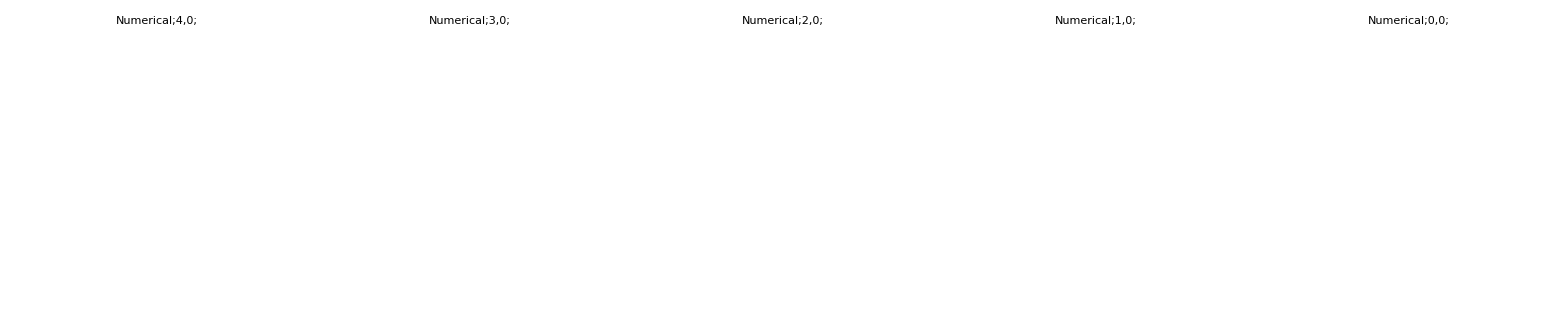

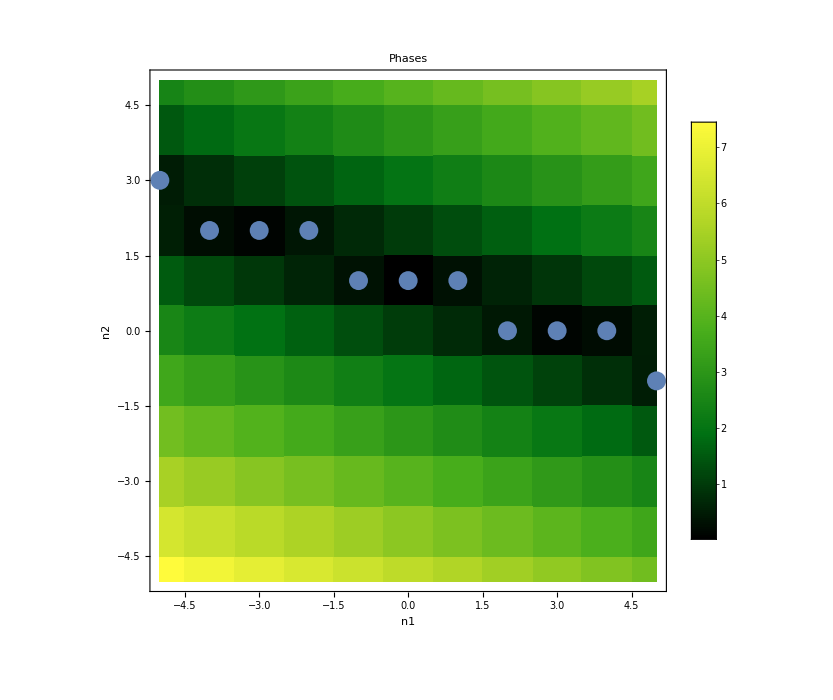
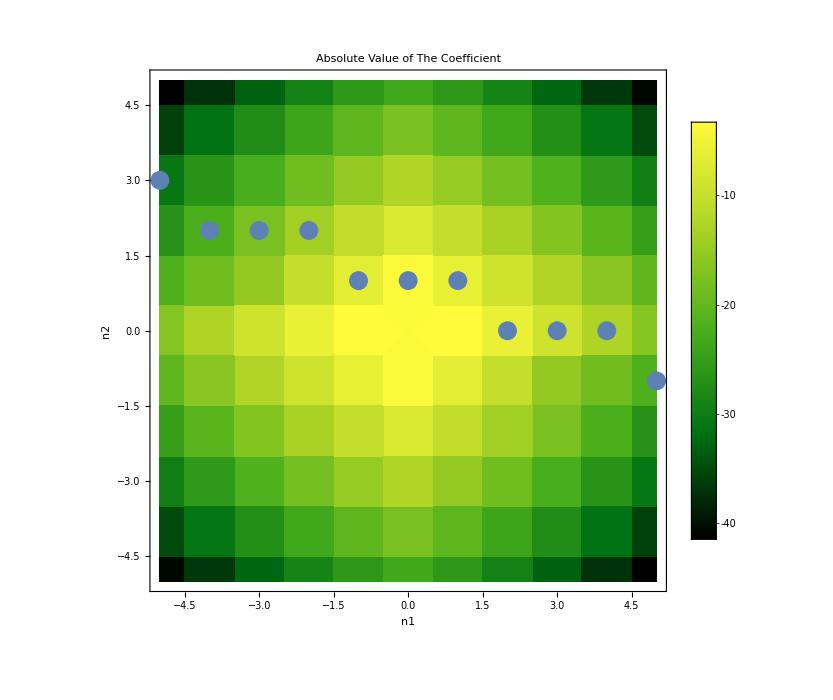
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{k1A,k2A,a1A,a2A,thetamA,range,range2},
k1A=0.3;
k2A=0.99;
a1A=0.2*0.1(k1A)^(-5/3);
a2A=0.1(k2A)^(-5/3);
thetamA=thetamV;
range=5;
range2=5 ;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,thetamA,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,thetamA,range,range2]
}}]
]
```

### Second Case

k1=0.3;
k2=0.99;
a1=0.4*0.1(k1)^(-5/3);
a2=0.1(k2)^(-5/3);

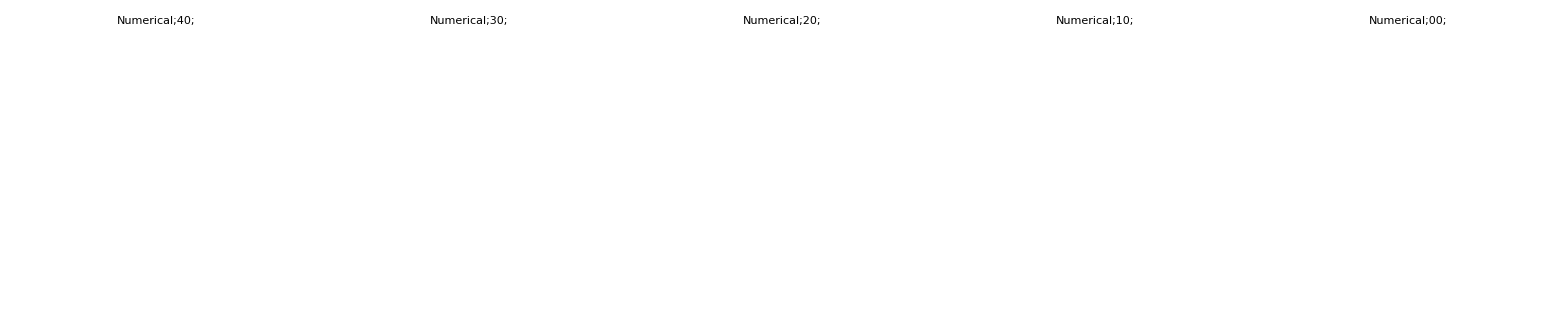

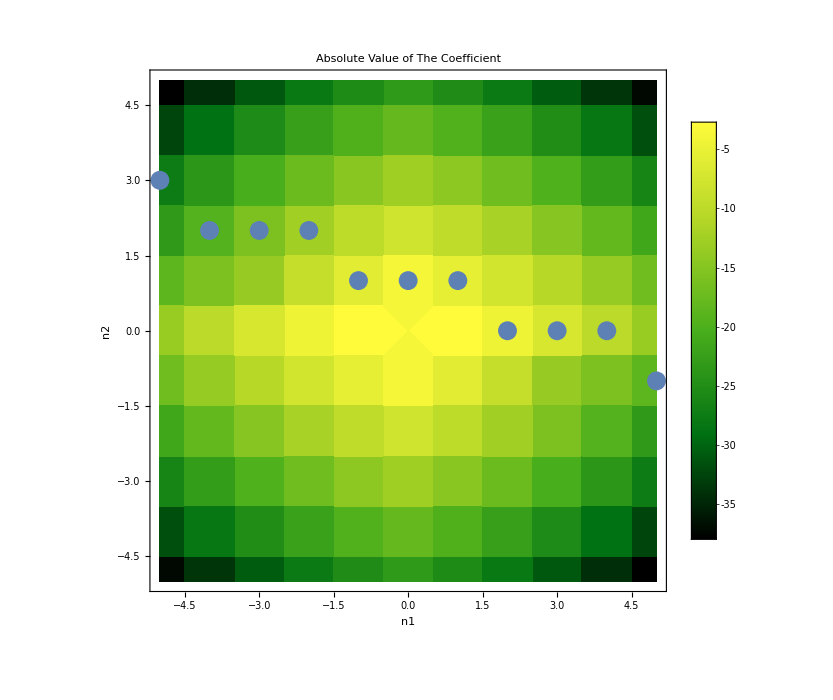
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{k1A,k2A,a1A,a2A,thetamA,range,range2},
k1A=0.3;
k2A=0.99;
a1A=0.4*0.1(k1A)^(-5/3);
a2A=0.1(k2A)^(-5/3);
thetamA=thetamV;
range=5;
range2=5 ;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,thetamA,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,thetamA,range,range2]
}}]
]
```

Resonances

```mathematica
amp2Freq[1.4,1,k1V,k2V,a1V,a2V,thetamV]
```

0.0000642386

```mathematica
Table[{n1Table,n2Fun[n1Table,k1V,k2V]},{n1Table,-3,3}]
```

{{-3,3},{-2,2},{-1,2},{0,1},{1,1},{2,1},{3,0}}

```mathematica
(*ToString[ToString[#,CForm]&/@qDis2Width[listOfn1n2Table[[1]],listOfn1n2Table[[2]],k1M,k2M,a1M,a2M,thetamM],Blue];*)
```

```mathematica
orderedQList[n1Range_,n2Range_,k1_,k2_,a1_,a2_,thetam_]:=SortBy[Flatten[Table[{{n1,n2},qDis2Width[n1,n2,k1,k2,a1,a2,thetam]},{n1,n1Range[[1]],n1Range[[2]]},{n2,n2Range[[1]],n2Range[[2]]}],1]//Quiet,Last];
Grid[orderedQList[{-3,3},{-3,3},k1V,k2V,a1V,a2V,thetamV]]
```

{1,1} | 0
{0,1} | 6.3263
{1,0} | 14.7294
{-1,0} | 27.3546
{0,-1} | 35.849
{2,0} | 136.214
{0,2} | 136.509
{-2,0} | 544.855
{3,0} | 653.176
{-1,2} | 670.569
{1,-1} | 708.477
{0,-2} | 819.056
{-1,-1} | 1012.11
{2,1} | 1219.5
{1,2} | 1776.49
{-2,-1} | 1958.43
{-2,2} | 2340.38
{2,3} | 2467.65
{-3,2} | 4816.36
{1,-2} | 6902.64
{0,3} | 7200.52
{-2,1} | 8528.96
{2,-1} | 11429.8
{2,2} | 11701.9
{-3,0} | 12410.3
{-1,-2} | 14214.9
{0,-3} | 20292.4
{-3,-1} | 29142.2
{-1,-3} | 56543.8
{3,1} | 59540.1
{3,-1} | 59953.9
{1,3} | 151152.
{1,-3} | 157296.
{-1,3} | 182068.
{-3,1} | 208157.
{2,-2} | 557089.
{-2,-2} | 928481.
{-2,3} | 1.66324×10^6
{-2,-3} | 1.66907×10^6
{3,2} | 1.72725×10^6
{3,-2} | 1.97857×10^6
{-3,3} | 2.07413×10^6
{-3,-2} | 2.17957×10^6
{2,-3} | 4.92942×10^6
{3,3} | 2.07413×10^7
{3,-3} | 4.2475×10^7
{-3,-3} | 7.72273×10^7
{-1,1} | ∞
{0,0} | ∞

```mathematica
Flatten[Table[{n1M,n2M},{n1M,-1,1},{n2M,-1,1}],1]
```

{{-1,-1},{-1,0},{-1,1},{0,-1},{0,0},{0,1},{1,-1},{1,0},{1,1}}

```mathematica
frameticksTest=Take[Table[{x,NumberForm[MeVInverse2km[x/OmegaMatter[thetamV,thetaV,omegaV]],2]},{x,0,1600}],{1,1600,Floor[(1600)/10]}]

(*frameTicks2freqMatterProfile=Take[Table[{x,MeVInverse2km[x/OmegaMatter[thetamM,thetaV,omegaV]]},{x,0,endpointM}],{1,endpointM,Floor[(endpointM)/10]}]*)
```

{{0,0.},{160,2.6×10^6},{320,5.2×10^6},{480,7.8×10^6},{640,1.×10^7},{800,1.3×10^7},{960,1.6×10^7},{1120,1.8×10^7},{1280,2.1×10^7},{1440,2.3×10^7}}

```mathematica
(*Show[Plot[x^2,{x,0,1600}],Framed->True,FrameTicks->{{Automatic,None},{Automatic,frameticksTest}}]*)
```

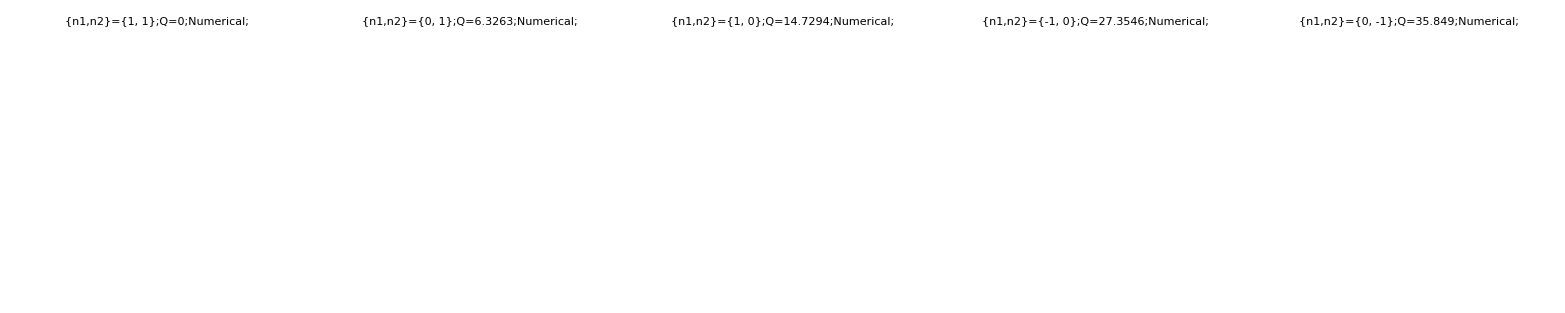
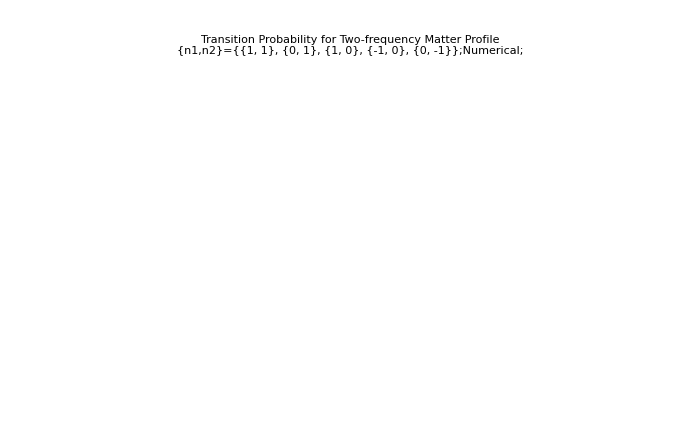

```mathematica
Module[{k1M,k2M,a1M,a2M,thetamM,endpointM,listOfn1n2,frameTicks2freqMatterProfile},
k1M=k1V;
k2M=k2V;
a1M=a1V;(*0.1(k1A)^(-5/3);*)
a2M=a2V;(*(k2A)^(-5/3);*)
thetamM=thetamV;
endpointM=1600;
(*listOfn1n2=Flatten[Table[{n1M,n2M},{n1M,-1,1},{n2M,-1,1}],1];*)
(*listOfn1n2={{1,1},{0,1},{1,0},{-1,0},{0,-1}};*)

listOfn1n2=Flatten[Drop[Part[orderedQList[{-3,3},{-3,3},k1M,k2M,a1M,a2M,thetamM],1;;5],None,{2}],1];

Grid[{
{
Grid[{Table[Show[plt0n1n2List[{listOfn1n2Table},k1M,k2M,a1M,a2M,thetamM,endpointM,"{n1,n2}="<>ToString[listOfn1n2Table]<>";Q="<>ToString[qDis2Width[listOfn1n2Table[[1]],listOfn1n2Table[[2]],k1M,k2M,a1M,a2M,thetamM]]<>";",Blue],pltN[k1M,k2M,a1M,a2M,thetamM,endpointM,{Red,Dashing[{0,0.01}]}],PlotRange->All,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontSize->14}],{listOfn1n2Table,listOfn1n2}]}]
},{
Show[plt0n1n2List[listOfn1n2,k1M,k2M,a1M,a2M,thetamM,endpointM,"{n1,n2}="<>ToString[listOfn1n2]<>";",Blue],pltN[k1M,k2M,a1M,a2M,thetamM,endpointM,{Red,Thickness[0.003],Dashing[{0.01,0.02}]}],PlotRange->All,LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontSize->14},PlotLabel->"Transition Probability for Two-frequency Matter Profile"]
}}]

]
```

Check Label with km

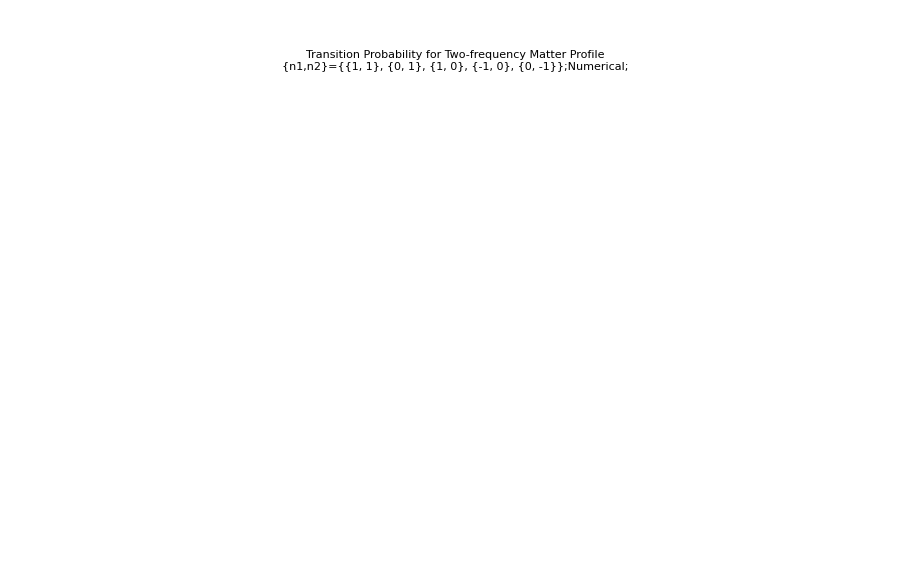

```mathematica
Module[{k1M,k2M,a1M,a2M,thetamM,endpointM,listOfn1n2,frameTicks2freqMatterProfile},
k1M=k1V;
k2M=k2V;
a1M=a1V;(*0.1(k1A)^(-5/3);*)
a2M=a2V;(*(k2A)^(-5/3);*)
thetamM=thetamV;
endpointM=1600;
(*listOfn1n2=Flatten[Table[{n1M,n2M},{n1M,-1,1},{n2M,-1,1}],1];*)
(*listOfn1n2={{1,1},{0,1},{1,0},{-1,0},{0,-1}};*)

listOfn1n2=Flatten[Drop[Part[orderedQList[{-3,3},{-3,3},k1M,k2M,a1M,a2M,thetamM],1;;5],None,{2}],1];

frameTicks2freqMatterProfile=Take[Table[{x,NumberForm[MeVInverse2km[x/OmegaMatter[thetamM,thetaV,omegaV]],2]},{x,0,endpointM}],{1,endpointM,Floor[(endpointM)/10]}];

Show[plt0n1n2List[listOfn1n2,k1M,k2M,a1M,a2M,thetamM,endpointM,"{n1,n2}="<>ToString[listOfn1n2]<>";",Blue,frameTicks2freqMatterProfile],pltN[k1M,k2M,a1M,a2M,thetamM,endpointM,{Red,Thickness[0.003],Dashing[{0.01,0.02}]}],PlotRange->All,LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontSize->14},PlotLabel->"Transition Probability for Two-frequency Matter Profile",ImagePadding->{{Automatic,Automatic},{Automatic,35}},ImageSize->imgsize*1.3]

]
```

Some Test

```mathematica
Module[{k1M,k2M,a1M,a2M,thetamM,endpointM,listOfn1n2},
k1M=k1V;
k2M=k2V;
a1M=a1V;(*0.1(k1A)^(-5/3);*)
a2M=a2V;(*(k2A)^(-5/3);*)
thetamM=thetamV;
endpointM=1600;
(*listOfn1n2=Flatten[Table[{n1M,n2M},{n1M,-0,1},{n2M,-1,1}],1];*)

listOfn1n2=Table[{n1Table,n2Fun[n1Table,k1M,k2M]},{n1Table,-3,3}];
(*listOfn1n2={{0,1},{1,1},{1,0}};*)

Grid[{{
amp2FreqContourPltList[listOfn1n2,k1V,k2V,a1V,a2V,thetamV,{0.01,2},{0.01,2}]
},{
Grid[{Table[Show[pltN[k1M,k2M,a1M,a2M,thetamM,endpointM,Red],plt0n1n2List[{listOfn1n2Table},k1M,k2M,a1M,a2M,thetamM,endpointM,"{n1,n2}="<>ToString[listOfn1n2Table]<>";Q="<>ToString[ToString[#,CForm]&/@qDis2Width[listOfn1n2Table[[1]],listOfn1n2Table[[2]],k1M,k2M,a1M,a2M,thetamM]],Blue],PlotRange->All],{listOfn1n2Table,listOfn1n2}]}]
}}]

]//Quiet
```

$Aborted

### More Manipulation

```mathematica
Limit[hamiltonian0[1,1,0.95,k2Limit,0.1,0,π/5],k2Limit->0]
```

0.

```mathematica
Manipulate[amp2FreqPlt[n1x,n2x,a1V,a2V,thetamV,{0.5,0.7},{0.0001,0.2}],{{n1x,1,"n1"},-10,10,1,Appearance->"Labeled"},{{n2x,1,"n2"},-10,10,1,Appearance->"Labeled"}];
```

```mathematica
kRangeV={0.01,2,0.01};
nRangeV={-1,1};
nRange2V={-2,2};
n1n2ListV= {{0,1},{1,1},{1,0}};
```

```mathematica
amp2FreqCombinedPlt[a1V,a2V,thetamV,kRangeV,kRangeV,nRangeV,nRangeV]
amp2FreqCombinedPlt[a1V,a2V,thetamV,kRangeV,kRangeV,nRange2V,nRange2V]
```

-Graphics-

-Graphics-

```mathematica
Show[amp2FreqCombinedPlt[a1V,a2V,thetamV,kRangeV,kRangeV,nRange2V,nRange2V],FrameLabel->{"(k̂)_1","(k̂)_2"},PlotLabel->"Density Plot of Transition Amplitudes",LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontWeight->"Bold",FontSize->18}]
```

-Graphics-

```mathematica
Export["export/density-plot-of-transition-amplitudes-demonstration.png",%]
```

export/density-plot-of-transition-amplitudes-demonstration.png

```mathematica
Show[amp2FreqCombinedPlt[a1V,a2V,thetamV,kRangeV,kRangeV,nRangeV,nRangeV],FrameLabel->{"(k̂)_1","(k̂)_2"},PlotLabel->"Density Plot of Transition Amplitudes",LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontWeight->"Bold",FontSize->18}]
```

-Graphics-

Draft

Test ordering algrimth

```mathematica
testList = {{{1,1},10},{{1,2},4},{{-1,3},30},{{0,1},7}}
```

{{{1,1},10},{{1,2},4},{{-1,3},30},{{0,1},7}}

```mathematica
SortBy[testList,Last]
```

{{{1,2},4},{{0,1},7},{{1,1},10},{{-1,3},30}}

```mathematica
Part[testList,1;;3]
Flatten[Drop[%,None,{2}],1]
```

{{{1,1},10},{{1,2},4},{{-1,3},30}}

{{1,1},{1,2},{-1,3}}